```mathematica
N0N[g_,x_]:=1/(1+(g*Exp[-x]))
```

```mathematica
N1N[g_,x_]:=(g*Exp[-x])*N0N[g,x]
```

```mathematica
Limit[N0N[2,x],x->0]
```

1/3

```mathematica
Limit[N0N[2,x],x->Infinity]
```

1

```mathematica
Limit[N1N[2,x],x->0]
```

2/3

```mathematica
Limit[N1N[2,x],x->Infinity]
```

0

```mathematica
plotN0N=Plot[N0N[2,x],{x,0,6},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0,6},{0,1}},Frame->True,FrameLabel->{Style["εβ = ε / kT",Bold,16],Style["Pᵢ = Nᵢ / N",Bold,16]},PlotLegends->{"P₀ = N₀/N"}];
```

```mathematica
plotN1N=Plot[N1N[2,x],{x,0,8},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Red,White}],Thick},PlotRange->{{0,6},{0,1}},Frame->True,FrameLabel->{Style["ε / kT",Bold,16]},PlotLegends->{"P₁ = N₁/N"}];
```

```mathematica
figmed=Plot[0.5,{x,0,40},PlotStyle->{Blend[{Black,White}],Dashed},PlotLegends->{"Pᵢ = 0.5"}];
```

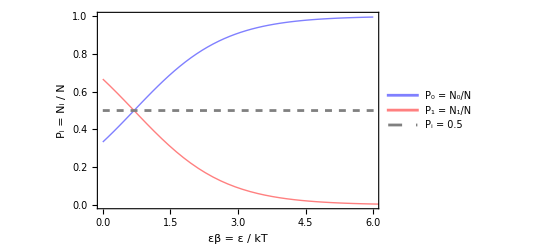

```mathematica
Show[plotN0N,plotN1N,figmed]
```

```mathematica
plotN0Ng=Plot[N0N[x,1],{x,0,40},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0,40},{0,1}},Frame->True,FrameLabel->{Style["g",Bold,16],Style["Pᵢ = Nᵢ / N",Bold,16]},PlotLegends->{"P₀ = N₀/N"}];
```

```mathematica
plotN1Ng=Plot[N1N[x,1],{x,0,40},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Red,White}],Thick},PlotRange->{{0,40},{0,1}},Frame->True,FrameLabel->{Style["ε / kT",Bold,16]},PlotLegends->{"P₁ = N₁/N"}];
```

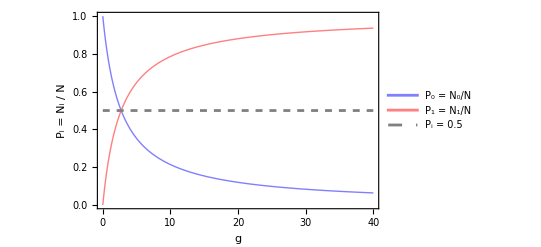

```mathematica
Show[plotN0Ng,plotN1Ng,figmed]
```

```mathematica
plotN0Nxg=Plot3D[N0N[x,y],{x,0,40},{y,0,6},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},ColorFunction->"BlueGreenYellow",AxesLabel->{Style["g",Bold,16],Style["εβ = ε / kT",Bold,16],Style[" P₀ = N₀/N",Bold,16]}]
```

-Graphics3D-

```mathematica
plotN1Nxg=Plot3D[N1N[x,y],{x,0,40},{y,0,6},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},ColorFunction->"BlueGreenYellow",AxesLabel->{Style["g",Bold,16],Style["εβ = ε / kT",Bold,16],Style[" P₁ = N₁/N",Bold,16]}]
```

-Graphics3D-

```mathematica
(*ENTROPÍA*)
```

```mathematica
SNK[x_,g_]:=x*Log[g]-x*Log[x]-(1-x)*Log[1-x]
```

```mathematica
plotSNK2=Plot[SNK[x,2],{x,0,1},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0,1},{0,2}},Frame->True,FrameLabel->{Style["E / Nε",Bold,16],Style["S / Nk",Bold,16]},PlotLegends->{"g = 2"}];
```

```mathematica
plotSNK1=Plot[SNK[x,1],{x,0,1},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Red,White}],Thick},PlotRange->{{0,1},{0,2}},Frame->True,FrameLabel->{Style["E / Nε",Bold,16],Style["S / Nk",Bold,16]},PlotLegends->{"g = 1"}];
```

```mathematica
plotSNK10=Plot[SNK[x,10],{x,0,1},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Black,White}],Thick},PlotRange->{{0,1},{0,2}},Frame->True,FrameLabel->{Style["E / Nε",Bold,16],Style["S / Nk",Bold,16]},PlotLegends->{"g = 10"}];
```

```mathematica
plotSNK5=Plot[SNK[x,5],{x,0,1},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Purple,White}],Thick},PlotRange->{{0,1},{0,2}},Frame->True,FrameLabel->{Style["E / Nε",Bold,16],Style["S / Nk",Bold,16]},PlotLegends->{"g = 5"}];
```

```mathematica
data={{0.5,SNK[0.5,1]},{2/3,SNK[2/3,2]},{5/6,SNK[5/6,5]},{10/11,SNK[10/11,10]}};
```

```mathematica
plotdata=ListPlot[data,PlotStyle->{Black,Thickness[0.003]}];
```

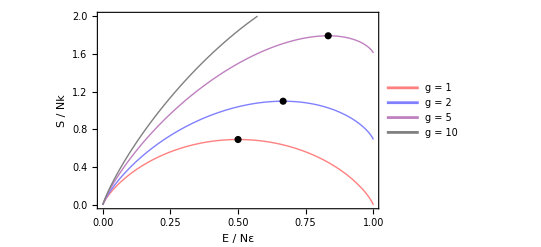

```mathematica
Show[plotSNK1,plotSNK2,plotSNK5,plotSNK10,plotdata]
```

```mathematica
p2=Plot[SNK[x,2],{x,0,1},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0,1},{0,1.2}},Frame->True,FrameLabel->{Style["E / Nε",Bold,16],Style["S / Nk",Bold,16]},Epilog->{InfiniteLine[{3/4,0},{0,1}]}];
```

```mathematica
data2={{2/3,SNK[2/3,2]}};
```

```mathematica
pdata2=ListPlot[data2,PlotStyle->{Black,Thickness[0.003]}];
```

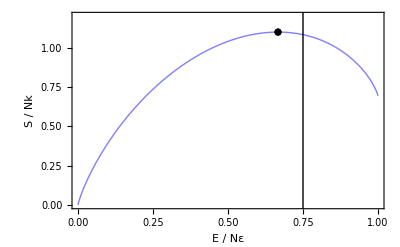

```mathematica
Show[p2,pdata2]
```

```mathematica
Emed[g_,T_]:=g*n*eps/(g+Exp[eps/(k*T)])
```

```mathematica
D[Emed[g,T],T]
```

(ⅇ^(eps/(k T)) eps^2 g n)/((ⅇ^(eps/(k T))+g)^2 k T^2)

```mathematica
Cv[x_,g_]:=g*Exp[x]*x^2/((g+Exp[x])^2)
```

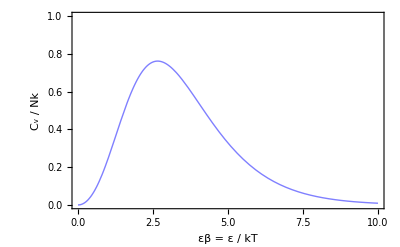

```mathematica
plotCv=Plot[Cv[x,2],{x,0,10},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0,10},{0,1}},Frame->True,FrameLabel->{Style["εβ = ε / kT",Bold,16],Style["Cᵥ / Nk",Bold,16]}]
```

```mathematica
Cv2[x_,g_]:=g*Exp[1/x]*(1/x)^2/((g+Exp[1/x])^2)
```

General::munfl: 9.58482×10^7 2.146954662×10^-8504 is too small to represent as a normalized machine number; precision may be lost.

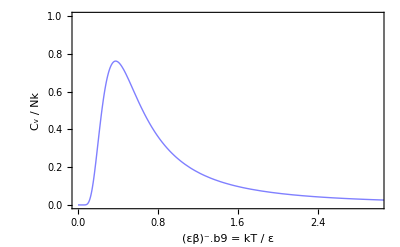

```mathematica
plotCv2=Plot[Cv2[x,2],{x,0,5},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{0,3},{0,1}},Frame->True,FrameLabel->{Style["(εβ)⁻.b9 = kT / ε",Bold,16],Style["Cᵥ / Nk",Bold,16]}]
```